```mathematica
Es1=Flatten[Import["/home/cjohns10/research/4BodySVD/ADeSpacings44-150x60x60x200x100-m12.dat"]];
Es2=Flatten[Import["/home/cjohns10/research/4BodySVD/ADeSpacings140-150x60x60x200x100-m12.dat"]];eTrim = Select[Es1,#>0.0000001&];
Length[Es]
Length[eTrim]
```

0

199

```mathematica
bins=Table[x,{x,0,5,0.2}];
```

```mathematica
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
```

```mathematica
EspaceBin1=BinCounts[eTrim,{bins}];
EspaceBin2=BinCounts[Es2,{bins}];
```

```mathematica
NormBrodyBinCs1=Table[EspaceBin1[[i]]/Total[EspaceBin1]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
NormBrodyBinCs2=Table[EspaceBin2[[i]]/Total[EspaceBin2]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
```

```mathematica
Remove[al,p]
```

```mathematica
alpha[q_]:=(Gamma[(q+2)/(q+1)])^(q+1)
```

```mathematica
p[q_,s_]:=alpha[q]*(q+1)*s^(q)*E^(-alpha[q]*s^(q+1))
```

```mathematica
brodyPdist1 = Table[{bFit[[i]],NormBrodyBinCs1[[i]]},{i,1,Length[bFit]}];
brodyPdist2 = Table[{bFit[[i]],NormBrodyBinCs2[[i]]},{i,1,Length[bFit]}];
```

```mathematica
p1=ListPlot[brodyPdist1,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Red];
p3=ListPlot[brodyPdist2,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Blue];
```

```mathematica
pars1 = FindFit[brodyPdist1,{p[q,s],q>0,q<1},{q},s]
pars2 = FindFit[brodyPdist2,{p[q,s],q>0,q<1},{q},s]
```

{q→0.417771}

{q→9.10352×10^-8}

```mathematica
p2=Plot[p[q/.pars1,s],{s,0,5},PlotRange->All,PlotStyle->Red];
p4=Plot[p[q/.pars2,s],{s,0,5},PlotRange->All,PlotStyle->Blue];
```

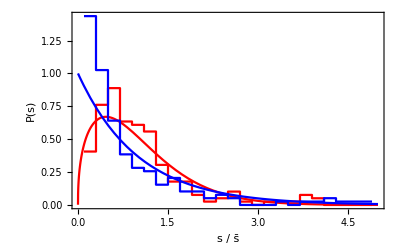

```mathematica
Show[p1,p2,p3,p4,PlotRange->All,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```

```mathematica
Export["/home/cjohns10/research/4BodySVD/ADenergiesHIST.pdf",%454,"PDF"]
```

/home/cjohns10/research/4BodySVD/ADenergiesHIST.pdf